```mathematica
ClearAll["Global`*"];
rawData = Import["/home/neophile/Documents/School/QEA/Ref frames/test-flight-1.csv"]; (*Import the data from a CSV, which was taken from a blackbox log*)
rawData = rawData[[2000;;]]; (*For large computations, cut the data down, or remove when the quad is on the ground*)
rawData = Transpose[rawData]; (*Easier to work with this way*)
columnsToUse = {2, 19, 20, 21, 22, 23, 24}; (*Others have things like barometer and stick positions*)
header = Transpose[rawData][[1]][[columnsToUse]] (*Roll, pitch, yaw*)
(*Gyro units are probably 1/16.384 degrees per second*)
(*Accel units are probably 1/2048 g*)
data = Transpose[Transpose[rawData[[columnsToUse]]][[2;;]]];(*Select the right columns*)
data[[1]] -= data[[1]][[1]]; (*Subtract the start time*)
data[[1]] /= 1000000; (*Microseconds to seconds*)
times = data[[1]];
tdiff = times[[2;;]] - times[[1;;Length[times]-1]]; (*Time differences*)
accel = Transpose[data[[{5, 6, 7}]]] * (1/2048) * (9.81); (*Convert to m/s^2*)
gyro = Transpose[data[[{2,3,4}]]] * (1/16.384) * (2*Pi/360); (*Convert to rads/s*)
```

{14979437,-11,0,0,186,-24,2368}

Null

```mathematica
i = {1,0,0}; (*World-frame basis*)
j = {0,1,0};
k = {0,0,1};

getPose[prevPose_, θi_, θj_, θk_] := RotationMatrix[θk, prevPose . k] . (RotationMatrix[θj, prevPose . j] . (RotationMatrix[θi, prevPose . i] . prevPose));

dir = {{i,j,k}}; (*Start pointing right side up, forwards.  Except we don't...*)
dθ = gyro[[2;;]] * tdiff; (*Adjust for time lengths*)
For[n=2,n<Length[dθ]+1,n++,dir=Evaluate[Append[dir, getPose[dir[[Length[dir]]], dθ[[n]][[1]], dθ[[n]][[2]], dθ[[n]][[3]]]]]]; (*Rotate each direction based on the previous directions*)
```

```mathematica
dv = accel[[2;;]] * tdiff;
dv2 = dv; (*Rotated direction changes*)
For[n=2,n<Length[dv],n++, dv2[[n]] = dir[[n]].dv[[n]]]; (*Rotate velocity changes based on which way the quad's pointing then*)
gravity = Table[9.81*k, Length[dv]] * tdiff;
dv -= gravity; (*Subtract gravity*)
dv2 -= gravity;

Assert[Length[tdiff] == Length[dv]];
v = Transpose[dv] . UpperTriangularize[ConstantArray[1,{Length[tdiff],Length[tdiff]}]];
v2 = Transpose[dv2] . UpperTriangularize[ConstantArray[1,{Length[tdiff],Length[tdiff]}]];

dp = Transpose[v] * tdiff;
p = Transpose[dp] . UpperTriangularize[ConstantArray[1,{Length[tdiff],Length[tdiff]}]];
dp2 = Transpose[v2] * tdiff;
p2 = Transpose[dp2] . UpperTriangularize[ConstantArray[1,{Length[tdiff],Length[tdiff]}]];
```

-Graphics3D-

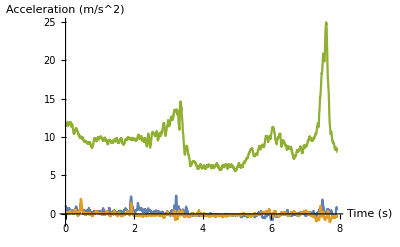

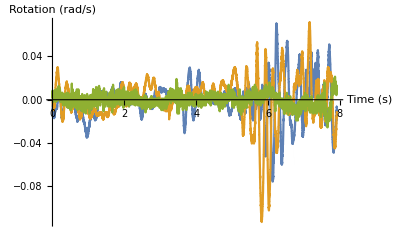

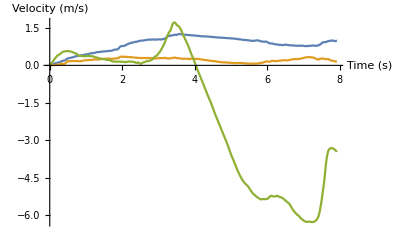

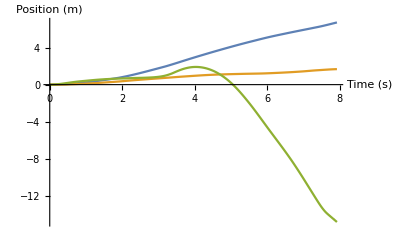

```mathematica
addTimes[in_] := Table[Transpose[{times[[1;;Length[in]]],Transpose[in][[m]]}], {m,1,3}];

ListPointPlot3D[Transpose[p2], AxesLabel->{"X (m)","Y (m)","Z (m)"}]
ListLinePlot[addTimes[accel], PlotRange->Full, AxesLabel->{"Time (s)", "Acceleration (m/s^2)"}]
ListLinePlot[addTimes[gyro], PlotRange -> Full, AxesLabel->{"Time (s)", "Rotation (rad/s)"}]
(*ListLinePlot[Transpose[(# . k) & /@ dir]]*)
(*ListLinePlot[v, PlotRange->{-4,2}]*)
ListLinePlot[addTimes[Transpose[v2]], PlotRange -> Full, AxesLabel->{"Time (s)", "Velocity (m/s)"}]
(*ListLinePlot[p]*)
ListLinePlot[addTimes[Transpose[p2]], PlotRange -> Full, AxesLabel->{"Time (s)", "Position (m)"}]
```